```mathematica
ClearAll["Global`*"]
```

#### Saving

```mathematica
NotebookDirectory[]
title="ps5_stability";
savename[specific_]:=StringJoin[NotebookDirectory[],"figures\\",title,"_",specific,".png"]

savename["test"]
```

C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\

C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_test.png

#### Laplace

```mathematica
lamat=({{s^2+n^2 kR, s n (kR-1)}, {-s n (kT-1), s^2+4 n^2 kT}});

Collect[Det[lamat],s]
schar=Collect[1/n^4 FullSimplify[Det[lamat]/.{s->sp n}/.{sp^2->s,sp^4->s^2}],s]
sollaplace=Solve[schar==0,s];
sollaplace[[1]][[1]][[2]]

(*{ContourPlot[Re[sollaplace[[1]][[1]][[2]]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All],ContourPlot[Im[sollaplace[[1]][[1]][[2]]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All]}
{ContourPlot[Re[sollaplace[[2]][[1]][[2]]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All],ContourPlot[Im[sollaplace[[2]][[1]][[2]]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All]}*)
```

4 kR kT n^4+(n^2+3 kT n^2+kR kT n^2) s^2+s^4

4 kR kT+(1+3 kT+kR kT) s+s^2

1/2 (-1-3 kT-kR kT-√(-16 kR kT+(1+3 kT+kR kT)^2))

Min[1/2 (-1+Re[-3 kT-kR kT-√(-16 kR kT+(1+3 kT+kR kT)^2)]),1/2 (-1+Re[-3 kT-kR kT+√(-16 kR kT+(1+3 kT+kR kT)^2)])]

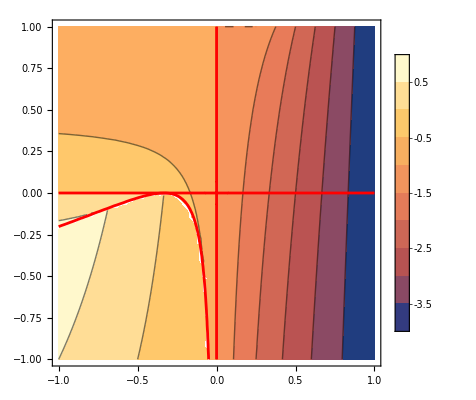

```mathematica
condfunclaplace=Min[Re[sollaplace[[1]][[1]][[2]]],Re[sollaplace[[2]][[1]][[2]]]]
Show[
ContourPlot[condfunclaplace,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All],
ContourPlot[(1+3kT+kT kR)^2-16 kR kT==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->Red],
ContourPlot[kR kT==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->Red]
]
```

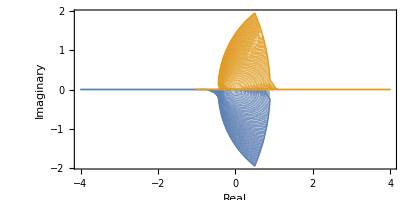

```mathematica
ParametricPlot[
Evaluate@Table[{Re[sollaplace[[k]][[1]][[2]]],Im[sollaplace[[k]][[1]][[2]]]},{k,1,2}],
{kR,-1,1},{kT,-1,1},
AxesLabel->{"Real","Imaginary"},FrameStyle->Black,AxesStyle->Black,
BoundaryStyle->Thick,MaxRecursion->3]
```

```mathematica
(*snosqchar=Collect[1/n^4 FullSimplify[Det[lamat]/.{s->sp n}],sp]
sollaplacenosq=Solve[snosqchar==0,sp];
sollaplacenosq
sollaplacenosq[[4]][[1]][[2]]

{ContourPlot[sollaplacenosq[[1]][[1]][[2]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic],
ContourPlot[sollaplacenosq[[2]][[1]][[2]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic],
ContourPlot[sollaplacenosq[[3]][[1]][[2]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic],
ContourPlot[sollaplacenosq[[4]][[1]][[2]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic]}*)
```

```mathematica
(*ParametricPlot[
Evaluate@Table[{Re[sollaplacenosq[[k]][[1]][[2]]],Im[sollaplacenosq[[k]][[1]][[2]]]},{k,1,4}],
{kR,-1,1},{kT,-1,1},
AxesLabel->{"Real","Imaginary"},FrameStyle->Black,AxesStyle->Black,
BoundaryStyle->Thick,MaxRecursion->3]
*)
```

```mathematica
(*Show[ContourPlot[Min[Table[Re[sollaplacenosq[[k]][[1]][[2]]],{k,1,4}]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,MaxRecursion->4],
ContourPlot[(1+3kT+kT kR)^2-16 kR kT==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->Red],
ContourPlot[kR kT==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->Red]]
*)
```

#### State Space Original

```mathematica
amatz=({{0, 1}, {3 n^2 kN, 0}})
Eigenvalues[amatz]
```

{{0,1},{3 kN n^2,0}}

{-√3 √kN n,√3 √kN n}

```mathematica
FullSimplify[kt-ix/iy kr/.{kn->(iy-ix)/iz,kt->(iz-ix)/iy,kr->(iz-iy)/ix}]
```

1-ix/iy

#### State Space

```mathematica
amat=({{0, 1, 0, 0}, {-n^2 kR, 0, 0, -n(kR-1)}, {0, 0, 0, 1}, {0, n(kT-1), -4 n^2 kT, 0}});
eiga=FullSimplify[Eigenvalues[amat],n>0]
FullSimplify[eiga/n,n>0]
FullSimplify[ExpandAll[(1+3 kT + kR kT)^2-16 kR kT]]
```

{-(√(-((1+(3+kR) kT+√(1+kT (6-14 kR+(3+kR)^2 kT))) n^2)))/(√2),(√(-((1+(3+kR) kT+√(1+kT (6-14 kR+(3+kR)^2 kT))) n^2)))/(√2),-(√(-1-(3+kR) kT+√(1+kT (6-14 kR+(3+kR)^2 kT))) n)/(√2),(√(-1-(3+kR) kT+√(1+kT (6-14 kR+(3+kR)^2 kT))) n)/(√2)}

{-(√(-1-(3+kR) kT-√(1+kT (6-14 kR+(3+kR)^2 kT))))/(√2),(√(-1-(3+kR) kT-√(1+kT (6-14 kR+(3+kR)^2 kT))))/(√2),-(√(-1-(3+kR) kT+√(1+kT (6-14 kR+(3+kR)^2 kT))))/(√2),(√(-1-(3+kR) kT+√(1+kT (6-14 kR+(3+kR)^2 kT))))/(√2)}

1+kT (6-14 kR+(3+kR)^2 kT)

```mathematica
eiga/.{n->1}
eiga/.{n->1,kT->1}
eiga/.{n->1,kT->0}
eiga/.{n->1,kR->0}
eiga/.{n->1,kT->0,kR->0}
```

{-(√(-1-(3+kR) kT-√(1+kT (6-14 kR+(3+kR)^2 kT))))/(√2),(√(-1-(3+kR) kT-√(1+kT (6-14 kR+(3+kR)^2 kT))))/(√2),-(√(-1-(3+kR) kT+√(1+kT (6-14 kR+(3+kR)^2 kT))))/(√2),(√(-1-(3+kR) kT+√(1+kT (6-14 kR+(3+kR)^2 kT))))/(√2)}

{-(√(-4-kR-√(7-14 kR+(3+kR)^2)))/(√2),(√(-4-kR-√(7-14 kR+(3+kR)^2)))/(√2),-(√(-4-kR+√(7-14 kR+(3+kR)^2)))/(√2),(√(-4-kR+√(7-14 kR+(3+kR)^2)))/(√2)}

{-ⅈ,ⅈ,0,0}

{-(√(-1-3 kT-√(1+kT (6+9 kT))))/(√2),(√(-1-3 kT-√(1+kT (6+9 kT))))/(√2),-(√(-1-3 kT+√(1+kT (6+9 kT))))/(√2),(√(-1-3 kT+√(1+kT (6+9 kT))))/(√2)}

{-ⅈ,ⅈ,0,0}

```mathematica
kRex=Range[-1,1,0.1]
eiga[[1]]/.{n->1,kT->1,kR->kRex}
```

{-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ,0.-2. ⅈ}

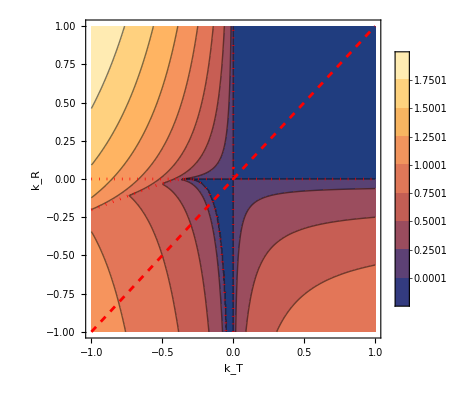

C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_stabilityplot.png

```mathematica
stabilityplot=Show[ContourPlot[Max[Re[eiga/.{n->1}]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,MaxRecursion->3,FrameLabel->{"k_T","k_R"},Contours->Table[k/4+0.0001,{k,0,8}],FrameStyle->Black],
(*ContourPlot[Max[Re[eiga/.{n->1}]]==0.001,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,MaxRecursion->5,FrameLabel->{"k_T","k_R"},Contours->Table[k/4,{k,-1,8}],ContourStyle->Thick],*)
ContourPlot[(1+3kT+kT kR)^2-16 kR kT==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->{Red,Dotted}],
ContourPlot[kR kT==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->{Red,Dotted}],
ContourPlot[kR -kT==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->{Red,Dashed}]]

Export[savename["stabilityplot"],stabilityplot,ImageResolution->300]
```

```mathematica
(*rootlocus2D=ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1}],Im[eiga[[k]]/.{n->1}]},{k,1,4}],
{kR,-1,1},{kT,-1,1},
PlotLegends->{"λ_1","λ_2","λ_3","λ_4"},
FrameLabel->{"Real","Imaginary"},FrameStyle->Black,AxesStyle->Black,
BoundaryStyle->Thick,MaxRecursion->6,PerformanceGoal->"Quality"]

Export[savename["rootlocus2D"],rootlocus2D,ImageResolution->300]*)
```

#### Static Versions

```mathematica
rlkTslice[kTSlice_,kRPoint_]:=Show[
{
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTSlice}],Im[eiga[[k]]/.{n->1,kT->kTSlice}]},{k,1,4}],
{kR,-1,1},
FrameLabel->{"Real","Imaginary"},FrameStyle->Black,AxesStyle->Black,
Frame->True,
PlotRange->{-2,2},
PlotLegends->{"λ_1","λ_2","λ_3","λ_4"}
],
ListPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTSlice,kR->kRPoint}],Im[eiga[[k]]/.{n->1,kT->kTSlice,kR->kRPoint}]},{k,1,4}],
AxesLabel->{"Real","Imaginary"},PlotStyle->{Black,PointSize[Large]}
]
}]

rlkRslice[kTPoint_,kRSlice_]:=Show[
{
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kR->kRSlice}],Im[eiga[[k]]/.{n->1,kR->kRSlice}]},{k,1,4}],
{kT,-1,1},
FrameLabel->{"Real","Imaginary"},FrameStyle->Black,AxesStyle->Black,
Frame->True,
PlotRange->{-2,2},
PlotLegends->{"λ_1","λ_2","λ_3","λ_4"}
],
ListPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kR->kRSlice,kT->kTPoint}],Im[eiga[[k]]/.{n->1,kR->kRSlice,kT->kTPoint}]},{k,1,4}],
AxesLabel->{"Real","Imaginary"},PlotStyle->{Black,PointSize[Large]}
]
}]

kbktslices[kTSlice_,kRSlice_]:=Show[ContourPlot[Max[Re[eiga/.{n->1}]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,MaxRecursion->3,FrameLabel->{"k_T","k_R"},Contours->Table[k/4+0.0001,{k,0,8}],FrameStyle->Black],
ContourPlot[kT-kTSlice==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->{White,Dashed}],
ContourPlot[kR-kRSlice==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->{White,DotDashed}],
ListPlot[
{{kTSlice,kRSlice}},
AxesLabel->{"Real","Imaginary"},PlotStyle->{Black,PointSize[Large]}
]
]
```

```mathematica
kTcritpt=-3/4
kRcritSol=FindRoot[Evaluate[(1+3kT+kT kR)^2-16 kR kT/.kT->kTcritpt]==0,{kR,0}]
kRcrit=kRcritSol[[1]][[2]]
```

-3/4

{kR→-0.113131}

-0.113131

```mathematica
kRbottomB=-1
kTcritSol=FindRoot[Evaluate[(1+3kT+kT kR)^2-16 kR kT/.kR->kRbottomB]==0,{kT,0}]
kTcrit=kTcritSol[[1]][[2]]
```

-1

{kT→-0.0505103}

-0.0505103

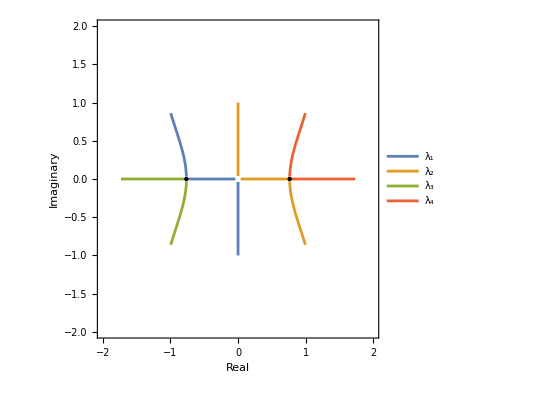
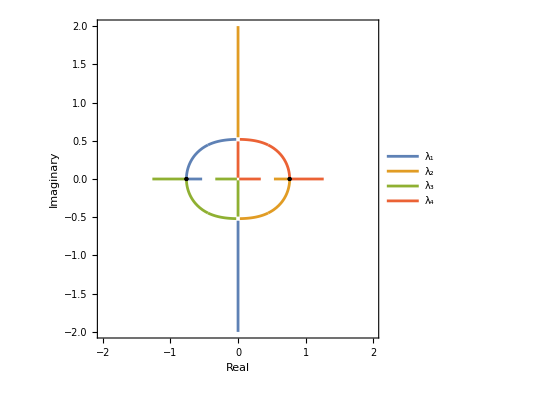
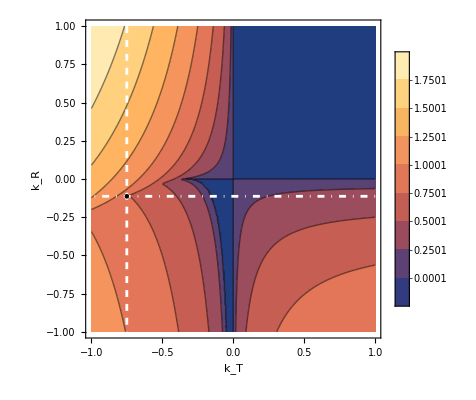
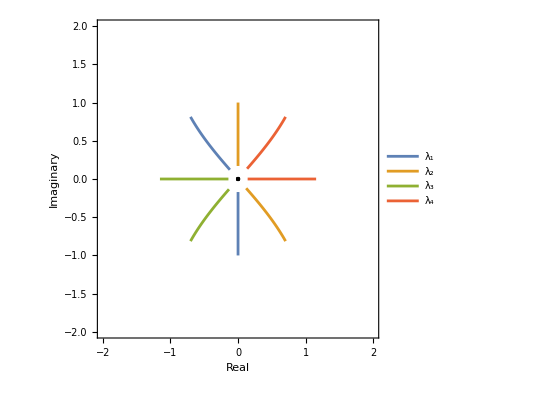
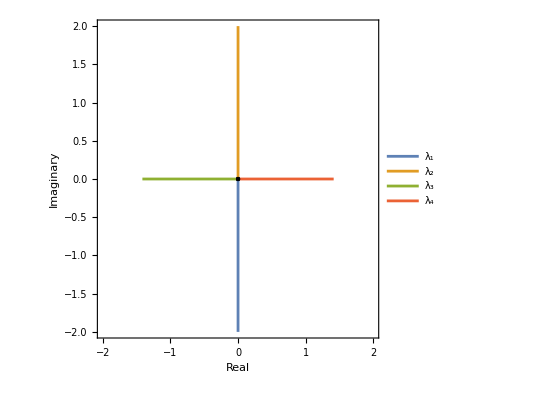
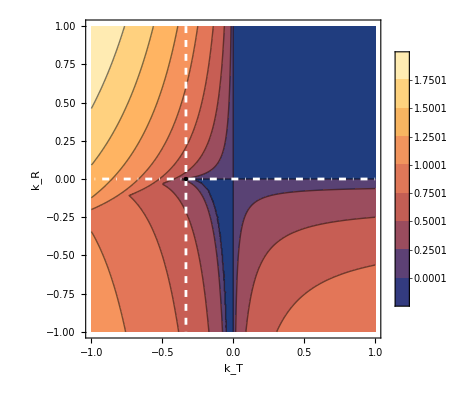
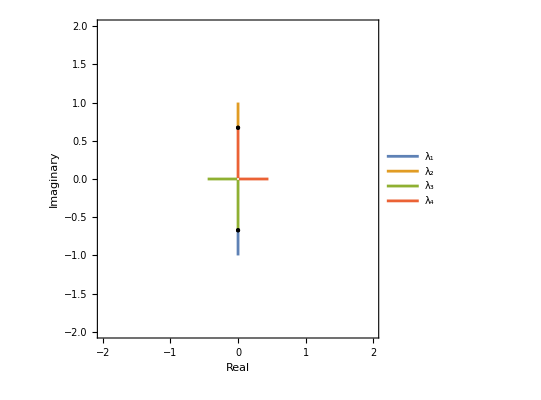
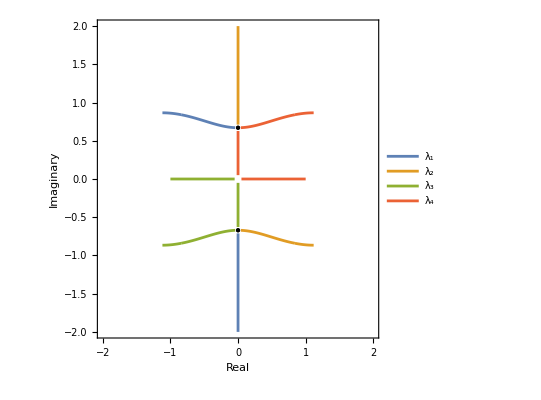

```mathematica
ktkbPairs={
{kTcritpt,kRcrit}, 
{-1/3,0},
{kTcrit,kRbottomB},
{1/2,1/4}};

rlociiTab=Table[{
rlkTslice[ktkbPairs[[k]][[1]],ktkbPairs[[k]][[2]]],
rlkRslice[ktkbPairs[[k]][[1]],ktkbPairs[[k]][[2]]],
kbktslices[ktkbPairs[[k]][[1]],ktkbPairs[[k]][[2]]]},
{k,1,Length[ktkbPairs]}]
```

```mathematica
Table[{
savename[StringJoin["rl_kTslice_",ToString[k]]],savename[StringJoin["rl_kRslice_",ToString[k]]],savename[StringJoin["rl_kTkR_",ToString[k]]]
},{k,1,Length[rlociiTab]}]
```

{{C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTslice_1.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kRslice_1.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTkR_1.png},{C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTslice_2.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kRslice_2.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTkR_2.png},{C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTslice_3.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kRslice_3.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTkR_3.png},{C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTslice_4.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kRslice_4.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTkR_4.png}}

```mathematica
Table[{
Export[savename[StringJoin["rl_kTslice_",ToString[k]]],rlociiTab[[k]][[1]],ImageResolution->300],
Export[savename[StringJoin["rl_kRslice_",ToString[k]]],rlociiTab[[k]][[2]],ImageResolution->300],
Export[savename[StringJoin["rl_kTkR_",ToString[k]]],rlociiTab[[k]][[3]],ImageResolution->300]
},{k,1,Length[rlociiTab]}]
```

{{C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTslice_1.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kRslice_1.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTkR_1.png},{C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTslice_2.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kRslice_2.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTkR_2.png},{C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTslice_3.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kRslice_3.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTkR_3.png},{C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTslice_4.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kRslice_4.png,C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rl_kTkR_4.png}}

#### Try out others

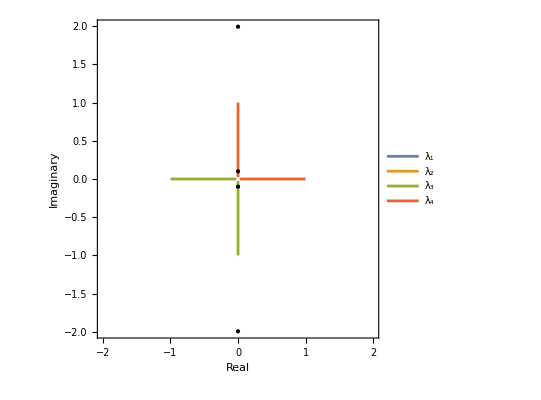
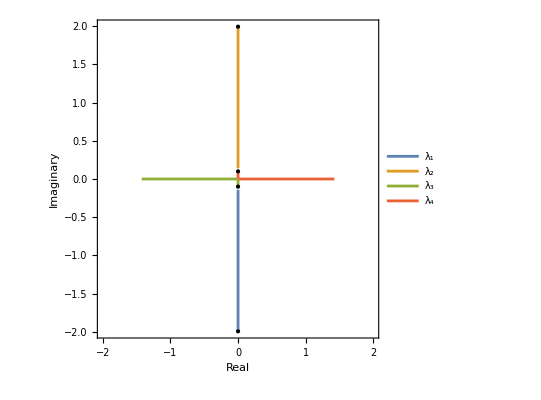
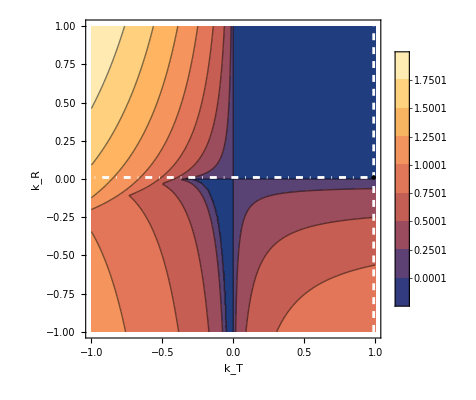

```mathematica
kttry=0.99;
krtry=0.01;

{rlkTslice[kttry,krtry],
rlkRslice[kttry,krtry],
kbktslices[kttry,krtry]}
```

#### Coefficients Check

```mathematica
ixyz={4770.398, 6313.894,7413.202};

krtn[rax_,tax_,nax_]:={(ixyz[[nax]]-ixyz[[tax]])/ixyz[[rax]],(ixyz[[nax]]-ixyz[[rax]])/ixyz[[tax]],(ixyz[[tax]]-ixyz[[rax]])/ixyz[[nax]]}

(*krtnbase={(ixyz[[3]]-ixyz[[2]])/ixyz[[1]],(ixyz[[3]]-ixyz[[1]])/ixyz[[2]],(ixyz[[2]]-ixyz[[1]])/ixyz[[3]]}

krtnxalong={(ixyz[[3]]-ixyz[[1]])/ixyz[[2]],(ixyz[[3]]-ixyz[[2]])/ixyz[[1]],(ixyz[[2]]-ixyz[[1]])/ixyz[[3]]}
krtnzearth={(ixyz[[2]]-ixyz[[1]])/ixyz[[3]],(ixyz[[2]]-ixyz[[3]])/ixyz[[1]],(ixyz[[1]]-ixyz[[3]])/ixyz[[2]]}
krtnxearth={(ixyz[[1]]-ixyz[[2]])/ixyz[[3]],(ixyz[[1]]-ixyz[[3]])/ixyz[[2]],(ixyz[[2]]-ixyz[[3]])/ixyz[[1]]}

krtnzalong={(ixyz[[1]]-ixyz[[3]])/ixyz[[2]],(ixyz[[1]]-ixyz[[2]])/ixyz[[3]],(ixyz[[2]]-ixyz[[3]])/ixyz[[1]]}
krtnyearth={(ixyz[[3]]-ixyz[[1]])/ixyz[[2]],(ixyz[[3]]-ixyz[[2]])/ixyz[[1]],(ixyz[[1]]-ixyz[[2]])/ixyz[[3]]}*)
krtnbase=krtn[1,2,3]
krtnxalong=krtn[2,1,3]
krtnzearth=krtn[3,1,2]
krtnxearth=krtn[1,3,2]

krtnzalong=krtn[2,3,1]
krtnyalong=krtn[3,2,1]

rtnNames={"Base^","x̂ || T","ẑ || R","x̂ || R","ẑ || T","ŷ || T"}
krtns={krtnbase,krtnxalong,krtnzearth,krtnxearth,krtnzalong,krtnyearth};
```

{0.230444,0.41857,0.208209}

{0.41857,0.230444,-0.208209}

{0.208209,-0.230444,-0.41857}

{-0.230444,0.208209,0.41857}

{-0.41857,-0.208209,0.230444}

{-0.208209,-0.41857,-0.230444}

{Base^,x̂ || T,ẑ || R,x̂ || R,ẑ || T,ŷ || T}

0.131848

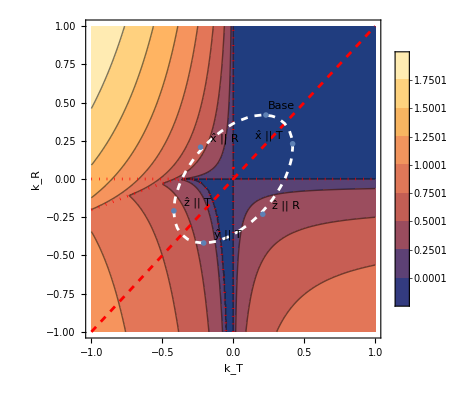

C:\Users\Daniel N\Desktop\GitHub\AA279C\mathematica\figures\ps5_stability_rtnpoints.png

```mathematica
kcritsqrd=kT^2-kR kT+kR^2/.{kT->krtnbase[[1]],kR->krtnbase[[2]]}

rtnpoints=Show[ContourPlot[Max[Re[eiga/.{n->1}]],{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,MaxRecursion->3,FrameLabel->{"k_T","k_R"},Contours->Table[k/4+0.0001,{k,0,8}],FrameStyle->Black],
ContourPlot[(1+3kT+kT kR)^2-16 kR kT==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->{Red,Dotted}],
ContourPlot[kR kT==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->{Red,Dotted}],
ContourPlot[kR -kT==0,{kT,-1,1},{kR,-1,1},PlotLegends->Automatic,PlotRange->All,ContourStyle->{Red,Dashed}],
ContourPlot[kT^2-kR kT+kR^2==0.1318,{kT,-1,1},{kR,-1,1},ContourStyle->{White,Dashed}],
ListPlot[Table[Labeled[krtns[[k,{1,2}]],rtnNames[[k]],Spacings->{Automatic}],{k,1,Length[krtns]}],PlotMarkers->{White,Large}]
]

Export[savename["rtnpoints"],rtnpoints,ImageResolution->300]
```

#### Manipulate Versions

```mathematica
(*Manipulate[Show[
ListPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}],Im[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}]},{k,1,4}],
AxesLabel->{"Real","Imaginary"},PlotStyle->{Black,Thick}]
],
{kTman,-1,1},{kRman,-1,1}
]
```

```mathematica
(*Manipulate[Show[
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{kT->kTman,kR->kRman}],Im[eiga[[k]]/.{kT->kTman,kR->kRman}]},{k,1,4}],
{n,0.1,6},
AxesLabel->{"Real","Imaginary"},PlotStyle->{Black,Thick}]
],
{kTman,-1,1},{kRman,-1,1}
]
*)
```

```mathematica
(*Manipulate[Show[
{
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman}],Im[eiga[[k]]/.{n->1,kT->kTman}]},{k,1,4}],
{kR,-1,1},
AxesLabel->{"Real","Imaginary"}
],
ListPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}],Im[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}]},{k,1,4}],
AxesLabel->{"Real","Imaginary"},PlotStyle->{Black,PointSize[Large]}
]
}],
{kTman,-1,1},{kRman,-1,1}
]
```

```mathematica
(*Manipulate[Show[
{
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kR->kRman}],Im[eiga[[k]]/.{n->1,kR->kRman}]},{k,1,4}],
{kT,-1,1},
AxesLabel->{"Real","Imaginary"}
],
ListPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}],Im[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}]},{k,1,4}],
AxesLabel->{"Real","Imaginary"},PlotStyle->{Black,PointSize[Large]}
]
}],
{kTman,-1,1},{kRman,-1,1}
]
*)
```

```mathematica
(*Manipulate[Show[
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman}],Im[eiga[[k]]/.{n->1,kT->kTman}]},{k,1,4}],
{kR,-1,1},
AxesLabel->{"Real","Imaginary"}]
],
{kTman,-1,1}
]
```

```mathematica
(*Manipulate[Show[
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kR->kRman}],Im[eiga[[k]]/.{n->1,kR->kRman}]},{k,1,4}],
{kT,-1,1},
AxesLabel->{"Real","Imaginary"}]
],{kRman,-1,1}
]
*)
```

```mathematica
(*Table[ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman}],Im[eiga[[k]]/.{n->1,kT->kTman}]},{k,1,4}],
{kR,-1,1},
AxesLabel->{"Real","Imaginary"},PlotRange->{-3,3}],
{kTman,-1,1,1/8}]
*)
```

```mathematica
(*Table[ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kR->kRman}],Im[eiga[[k]]/.{n->1,kR->kRman}]},{k,1,4}],
{kT,-1,1},
AxesLabel->{"Real","Imaginary"},PlotRange->{-3,3}],
{kRman,-1,1,1/8}]*)
```